# Obtenção da Ynodal para um dos circuitos da LT Norte Sul

tem erro na altura média dos condutores

```mathematica
Clear["Global`*"]
```

supondo a Lt idealmente transposta

```mathematica
SetOptions[{ListPlot,ListLogLinearPlot,ListLogPlot},Frame->True,Axes->False,ImageSize->600,Joined->True,PlotStyle->{Thick},BaseStyle->{Medium,FontFamily->"Times"}];
```

## Funções Auxiliares

```mathematica
μ=4 π 10^-7;
ϵ=8.854 10^-12;
```

```mathematica
(*rotinas para o calculo dos parametros unitarios de uma LT*)
inv[m_?MatrixQ,a_,b_]:=Take[Inverse[m],a,b]

eliminaPR[m_?MatrixQ,nc_,np_]:=Take[Inverse[m],nc-np,nc-np]

(*eliminacao de feixes mas a matriz deve estar como admitancia*)
eliminaFeixe[aux_?MatrixQ,nb_,nf_]:=Table[Sum[aux[[i,j]],{i,nb*m-(nb-1),nb*m},{j,nb*n-(nb-1),nb*n}],{m,nf},{n,1,nf}]

(*monta a matriz de coeficientes de potencial*)
MPot[x_?VectorQ,y_?VectorQ,nc_,npr_,rf_,rpr_]:=Table[If[i≠j,1/2 Log[((x[[i]]-x[[j]])^2+(y[[i]]+y[[j]])^2)/((x[[i]]-x[[j]])^2+(y[[i]]-y[[j]])^2)],If[i≤nc-npr,Log[2 y[[i]]/rf],Log[2 y[[i]]/rpr]]],{i,1,nc},{j,1,nc}]

(*impedancia interna de condutores cilindricos*)
ZintTubo[omega_,rhoc_,rf_,ri_,mu_: 4 Pi 10^-7]:=With[{etac=Sqrt[(I omega mu)/rhoc]//N},With[{Den=BesselI[1,etac rf] BesselK[1,etac ri]-BesselI[1,etac ri] BesselK[1,etac rf],Num=(BesselI[0,etac rf] BesselK[1,etac ri]+BesselK[1,etac rf] BesselI[1,etac ri])},(rhoc etac)/(2 π rf) Num/Den]]

ZintTubo2[omega_,rhoc_,rf_,ri_,mu_: 4 Pi 10^-7]:=With[{Den=BesselI[1,Sqrt[(I omega mu)/rhoc] rf]*BesselK[1,Sqrt[(I omega mu)/rhoc] ri]-BesselI[1,Sqrt[(I omega mu)/rhoc] ri]*BesselK[1,Sqrt[(I omega mu)/rhoc] rf]//N,Num=(BesselI[0,Sqrt[(I omega mu)/rhoc] rf]*BesselK[1,Sqrt[(I omega mu)/rhoc] ri]+BesselK[1,Sqrt[(I omega mu)/rhoc] rf]*BesselI[1,Sqrt[(I omega mu)/rhoc] ri]//N)},(rhoc Sqrt[(I omega mu)/rhoc])/(2 Pi rf) Num/Den]

Zexterno[omega_,sigma_,ncond_,npr_,(x_)?VectorQ,(y_)?VectorQ,rf_,rpr_,mu_: (4*Pi)/10^7,mupr_: (4*Pi)/10^7]:=With[{p=Sqrt[1/(I*omega*mu*sigma)]},Table[If[i≠j,((I*omega*mu)/(4*Pi))*Log[((x[[i]]-x[[j]])^2+(2*p+y[[i]]+y[[j]])^2)/((x[[i]]-x[[j]])^2+(y[[i]]-y[[j]])^2)],If[i≤ncond-npr,((I*omega*mu)/(2*Pi))*Log[(2*(y[[i]]+p))/rf],((I*omega*mu)/(2*Pi))*Log[(2*(y[[i]]+p))/rpr]]],{i,1,ncond},{j,1,ncond}]]


(*impedancia interna de condutores cilindricos*)

Zin[Omega_,Rhopr_,rpr_,Mur_: 80,Mupr_: (4*Pi)/10^7]:=With[{Etapr=Sqrt[(I*Omega*Mur*Mupr)/Rhopr]},((Etapr*Rhopr)*BesselI[0,Etapr*rpr])/((2*Pi*rpr)*BesselI[1,Etapr*rpr])]

(*rotinas para copiar o linspace e o logspace do matlab*)

freqlog[i_,f_,np_]:=Table[N[10^(i+(x*(f-i))/(Floor[np]-1))],{x,0,np-1}]

freqlin[i_,f_,np_]:=Table[N[i+(x*(f-i))/(Floor[np]-1)],{x,0,np-1}]

(*Calculo da matriz de admitancia nodal a partir de parametros unitarios e comprimento do circuito*)Ynodal[Z_,Y_,length_]:=Module[{Z1=Z,Y1=Y,eval,evect,d,Tv,Tvi,hm,Am,Bm,y11,y12,Yy},{eval,evect}=Eigensystem[N[Z1.Y1]];
d=Sqrt[eval];
Tv=Transpose[evect];
Tvi=Inverse[Transpose[evect]];
hm=Exp[-d*length];
Am=d*(1+hm^2)/(1-hm^2);
Bm=-2.0*d*hm/(1-hm^2);
y11=N[Inverse[Z1]].Tv.DiagonalMatrix[Am].Tvi;
y12=N[Inverse[Z1]].Tv.DiagonalMatrix[Bm].Tvi;
Yy=ArrayFlatten[{{y11,y12},{y12,y11}}]]


(*funcao para conversao de Ynodal simetrica para quadripolo*)
Y2Quad[ynodal_]:=Module[{n,y11,y12,aux,AA,BB,CC},n=Length[ynodal];
y11=ynodal[[Range[1,n/2],Range[1,n/2]]];
y12=ynodal[[Range[1,n/2],Range[n/2+1,n]]];
aux=Inverse[y12];
AA=-aux.y11;
BB=-aux;
CC=y12-y11.aux.y11;
Qout=ArrayFlatten[{{AA,BB},{CC,AA}}]]
```

## Configuração da LT

```mathematica
xy= {{-4.271, 10.771}, {-4.271, 11.229}, {-4.729, 11.229}, {-4.729, 10.771}, {0.229, 15.271},
{0.229, 15.729}, {-0.229, 15.729}, {-0.229, 15.271}, {4.271, 10.771}, {4.271, 11.229},{4.729, 11.229},{4.729, 10.771}, {-3.500, 26.000}, {3.500, 26.000}};
```

```mathematica
mostra1={Circle[#,.25]}&/@xy;
```

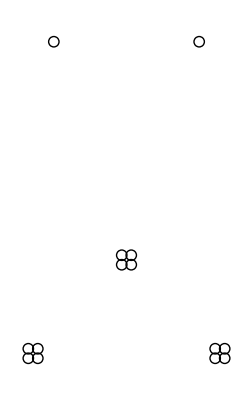

```mathematica
t1=Show[Graphics[mostra1],AspectRatio->Automatic,Axes->False,Frame->Automatic,FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
xc=xy[[All,1]];
```

```mathematica
yc=xy[[All,2]];
```

```mathematica
ncond=Length[xc];
npr=2;
nfeixe=4;
nfases=3;
```

```mathematica
rf=29.591*10^-3/2;
r0=(7.3914/2*10^-3);
ρc=6.114292531162*10^-5 Pi*(rf^2-r0^2);
rpr=4.57*10^-3;
Rdcpr=4.19*10^-3;
ρpr=Rdcpr*Pi*rpr^2;
ρsolo=1000.;
σsolo=1/ρsolo;
```

### Resposta em Frequência

```mathematica
f=Sort[Join[freqlog[-1,5,500],freqlin[.1, 1000.,500]]];
ℓ=343/6;
nf=Length[f];
```

```mathematica
yr=1/(3+I ω 5304.4 10^-3);
zc=1-I/(ω  42017/(2 π 60.) 10^-6);
zero=DiagonalMatrix[{0,0,0}];
eye=DiagonalMatrix[{1,1,1}];
```

```mathematica
Qreator=ArrayFlatten[{{eye,zero},
                                            {DiagonalMatrix[{yr,yr,yr}],eye}}];
```

```mathematica
Qcap=ArrayFlatten[{{eye,DiagonalMatrix[{zc,zc,zc}]},
{zero,eye}}];
```

```mathematica
ϕ1={{0,1,0},{0,0,1},{1,0,0}};
```

```mathematica
Qϕ=ArrayFlatten[{{ϕ1,zero},{zero,ϕ1}}];
a=Exp[I 120 Degree];
A1={{1,1,1},{1,a^2,a},{1,a,a^2}};
Aaux=ArrayFlatten[{{A1,zero},{zero,A1}}];
```

```mathematica
ylt=Table[0,{nf}];
```

```mathematica
AbsoluteTiming[Do[{ω=2 π f[[k]],
aux0=DiagonalMatrix[
      Table[If[i≤(ncond-2),
        Zin[ω,ρc,rf,1],
        Zin[ω,ρpr,rpr,80.]],{i,ncond}]];
aux1=ⅉ ω 2 π ϵ eliminaPR[MPot[xc,yc,ncond,2,rf,rpr],ncond,2];
aux2=aux0+ Zexterno[ω,σsolo,ncond,2,xc,yc,rf,rpr],
Y0=eliminaFeixe[aux1,nfeixe,nfases];
Z0=Inverse[eliminaFeixe[eliminaPR[aux2,ncond,2],nfeixe,nfases]],
Y1=Table[If[i≠ j,Tr[Y0]/3,(Y0[[1,2]]+Y0[[1,3]]+Y0[[2,3]])/3],{i,3},{j,3}];
Z1=Table[If[i≠ j,Tr[Z0]/3,(Z0[[1,2]]+Z0[[1,3]]+Z0[[2,3]])/3],{i,3},{j,3}],
ylt1=Ynodal[Z1,Y1,343],
Qlt1=Y2Quad[ylt1],
Qt=Qcap.Qreator.Qlt1.Qreator.Qcap,
Aeq=Qt[[Range[3],Range[3] ]],
Beq=Qt[[Range[3],Range[4,6] ]],
Ceq=Qt[[Range[4,6],Range[3] ]],
Deq=Qt[[Range[4,6],Range[4,6] ]],
aux2=Inverse[Beq],
y11eq=Deq.aux2,
y12eq=Ceq-Deq.aux2. Aeq,
y21eq=-aux2,
y22eq=aux2.Aeq,
yaux=ArrayFlatten[{{y11eq,y12eq},{y21eq,y22eq}}] ,
ylt[[k]] =Inverse[Aaux].yaux.Aaux

},

{k,1,nf}]]
```

{14.09562,Null}

```mathematica
yplota=Transpose@Flatten[Transpose[ylt,{3,1,2}],1];
```

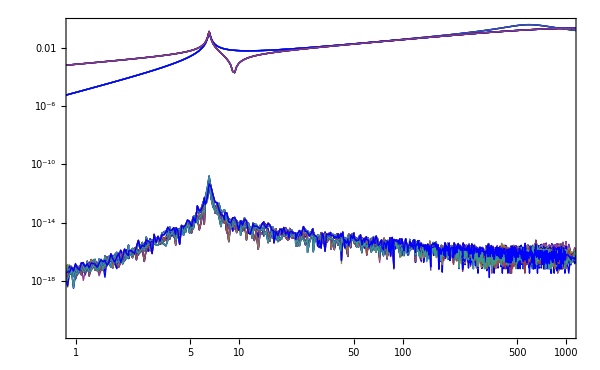

```mathematica
ListLogLogPlot[Table[Transpose@{f,Abs[yplota[[All,i]]]},{i,36}],Joined-> True,Frame-> True,PlotStyle-> {Blue,Thick},PlotRange-> {{1,1000},All}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/acsl/Dropbox/orientados/cesar

```mathematica
Export["yNSidT.mat",yplota]
```

yNSidT.mat

```mathematica
Export["freq.mat",f]
```

freq.mat

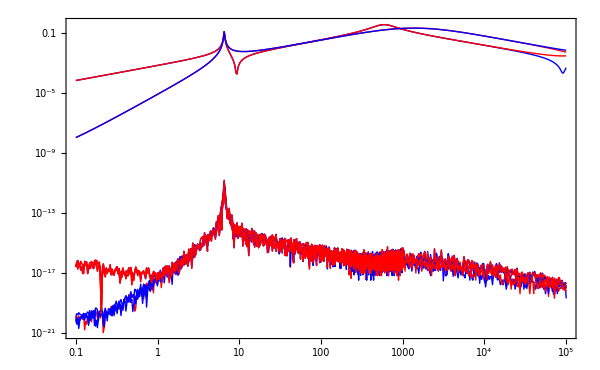

```mathematica
ListLogLogPlot[{
Transpose@{f,Abs[ylt[[All,1,1]] ]},
Transpose@{f,Abs[ylt[[All,1,2]] ]},
Transpose@{f,Abs[ylt[[All,1,3]] ]},
Transpose@{f,Abs[ylt[[All,1,4]] ]},
Transpose@{f,Abs[ylt[[All,1,5]] ]},
Transpose@{f,Abs[ylt[[All,1,6]] ]},
Transpose@{f,Abs[ylt[[All,2,1]] ]},
Transpose@{f,Abs[ylt[[All,2,2]] ]},
Transpose@{f,Abs[ylt[[All,2,3]] ]},
Transpose@{f,Abs[ylt[[All,2,4]] ]},
Transpose@{f,Abs[ylt[[All,2,5]] ]},
Transpose@{f,Abs[ylt[[All,2,6]] ]}
}
,PlotRange-> All,Joined-> True,
PlotStyle->{Table[{Blue,Thick},{6}],
                       Table[{Red,Thick},{6}]
},
Frame-> True]
```

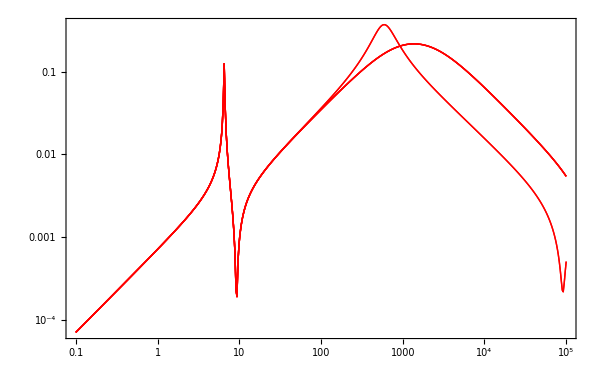

```mathematica
ListLogLogPlot[{
Transpose@{f,Abs[ylt[[All,1,1]] ]},
Transpose@{f,Abs[ylt[[All,2,2]] ]},
Transpose@{f,Abs[ylt[[All,3,3]] ]},
Transpose@{f,Abs[ylt[[All,4,4]] ]},
Transpose@{f,Abs[ylt[[All,5,5]] ]},
Transpose@{f,Abs[ylt[[All,6,6]] ]}
}
,PlotRange-> All,Joined-> True,PlotStyle->{{Red,Thick}},Frame-> True]
```

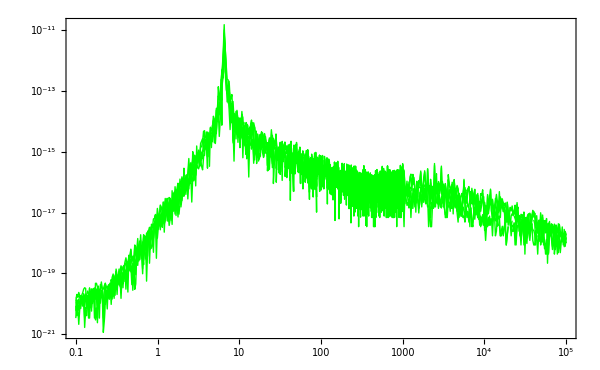

```mathematica
ListLogLogPlot[{
Transpose@{f,Abs[ylt[[All,2,1]] ]},
Transpose@{f,Abs[ylt[[All,1,2]] ]},
Transpose@{f,Abs[ylt[[All,2,3]] ]},
Transpose@{f,Abs[ylt[[All,3,2]] ]},
Transpose@{f,Abs[ylt[[All,1,3]] ]},
Transpose@{f,Abs[ylt[[All,3,1]] ]}
}
,PlotRange-> All,Joined-> True,PlotStyle->{{Green,Thick}},Frame-> True]
```

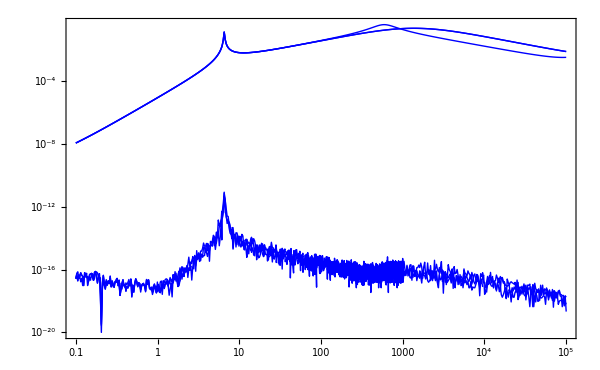

```mathematica
ListLogLogPlot[{
Transpose@{f,Abs[ylt[[All,1,4]] ]},
Transpose@{f,Abs[ylt[[All,2,5]] ]},
Transpose@{f,Abs[ylt[[All,3,6]] ]},
Transpose@{f,Abs[ylt[[All,1,5]] ]},
Transpose@{f,Abs[ylt[[All,2,4]] ]},
Transpose@{f,Abs[ylt[[All,3,5]] ]}
}
,PlotRange-> All,Joined-> True,PlotStyle->{{Blue,Thick}},Frame-> True]
```

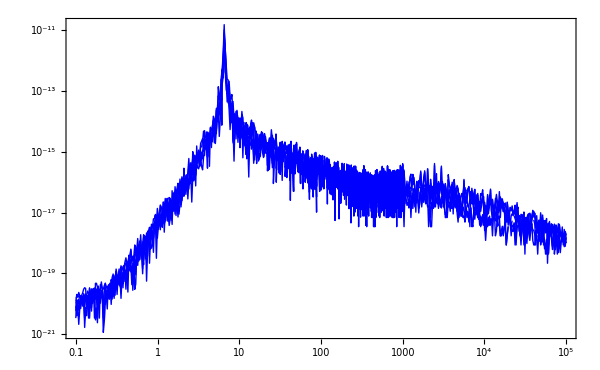

```mathematica
ListLogLogPlot[{
Transpose@{f,Abs[ylt[[All,1,3]] ]},
Transpose@{f,Abs[ylt[[All,1,2]] ]},
Transpose@{f,Abs[ylt[[All,3,1]] ]},
Transpose@{f,Abs[ylt[[All,3,2]] ]},
Transpose@{f,Abs[ylt[[All,2,3]] ]},
Transpose@{f,Abs[ylt[[All,2,1]] ]}
}
,PlotRange-> All,Joined-> True,PlotStyle->{{Blue,Thick}},Frame-> True]
```

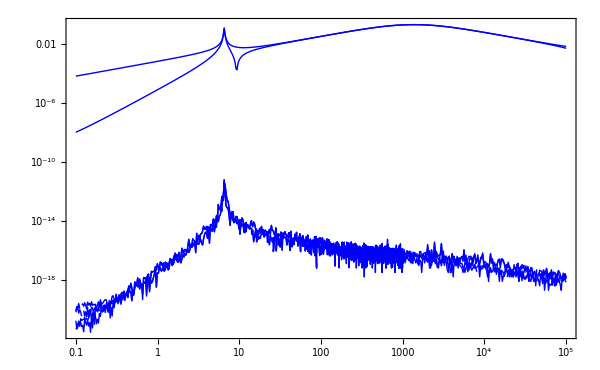

```mathematica
ListLogLogPlot[{
Transpose@{f,Abs[ylt[[All,6,1]] ]},
Transpose@{f,Abs[ylt[[All,6,2]] ]},
Transpose@{f,Abs[ylt[[All,6,3]] ]},
Transpose@{f,Abs[ylt[[All,6,4]] ]},
Transpose@{f,Abs[ylt[[All,6,5]] ]},
Transpose@{f,Abs[ylt[[All,6,6]] ]}
}
,PlotRange-> All,Joined-> True,PlotStyle->{{Blue,Thick}},Frame-> True]
```

```mathematica
Dimensions[ylt[[All,1,All]]]
```

{1000,6}